```mathematica
Quit;
```

```mathematica
ClearAll;
cm=72/2.54;
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/pdflatex","Ghostscript"->"/usr/local/bin/gs"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
<<MaTeX`
```

ConfigureMaTeX[pdfLaTeX→/usr/bin/pdflatex,Ghostscript→/usr/local/bin/gs]

MaTeX::shdw: Symbol "MaTeX" appears in multiple contexts {"MaTeX`", "Global`"}; definitions in context "MaTeX`" may shadow or be shadowed by other definitions.

ConfigureMaTeX::shdw: Symbol "ConfigureMaTeX" appears in multiple contexts {"MaTeX`", "Global`"}; definitions in context "MaTeX`" may shadow or be shadowed by other definitions.

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}"}]
```

{Preamble→{\usepackage{amsmath,amssymb}},DisplayStyle→True,FontSize→12,Magnification→1}

```mathematica
Action = (((r*Sin[θ[r]])^2)*((1+(r^2))^(-1)+((r*(θ'[r]))^2)))^(1/2)
```

√(r^2 Sin[θ[r]]^2 (1/(1+r^2)+r^2 θ'[r]^2))

```mathematica
RHSr = FullSimplify[D[Action,θ[r]]]; (*Compute Euler Lagrange Equations*)
```

```mathematica
LHSr=FullSimplify[Dt[D[Action,θ'[r]],r]];
```

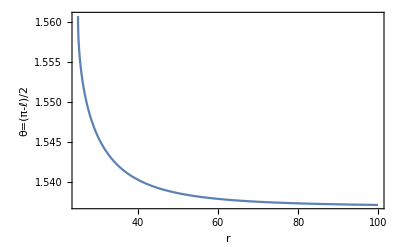

```mathematica
r0j=25;
Jointed = NDSolve[{RHSr==LHSr,θ[r0j]==Pi/2-0.01,θ'[r0j]==-80},θ,{r,r0j,100}]; 
(*Solve for the solution which does not cross θ=0*)
Plot[Evaluate[θ[r]/.Jointed],{r,r0j,100},PlotRange->All,Frame->True,FrameLabel->{"r","θ=(π-ℓ)/2"}]
```

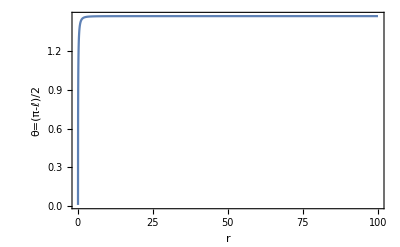

```mathematica
r0d=0.1;
DisJointed = NDSolve[{RHSr==LHSr,θ[r0d]==0.01,θ'[r0d]==80},θ,{r,r0d,100}];(*Solve for the solution which crosses from one side at θ=0 r =r0 *)
Plot[Evaluate[θ[r]/.DisJointed],{r,r0d,100},PlotRange->All,Frame->True,FrameLabel->{"r","θ=(π-ℓ)/2"}]
```

```mathematica
beg=0.01;
end=10.0;
step=0.01;
```

```mathematica
JointedTab=Flatten[Table[{(Pi/2-θ[100]),r0}/.NDSolve[{RHSr==LHSr,θ[r0]==Pi/2-0.0001,θ'[r0]==-80},θ,{r,r0,1000}],{r0,beg,end,step}],1];
```

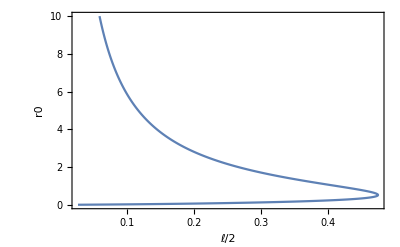

```mathematica
ListLinePlot[JointedTab,PlotRange->All,Frame->True,FrameLabel->{"ℓ/2","r0"}] 
(*Plot the variation of ℓ/2 with r for the jointed solution. we see that ℓ/2 is bounded between 0 and ~0.5rad*)
```

```mathematica
DisJointedTab=Flatten[Table[{Pi/2-θ[100],r0}/.NDSolve[{RHSr==LHSr,θ[r0]==0.001,θ'[r0]==80},θ,{r,r0,1000}],{r0,beg,end,step}],1];
```

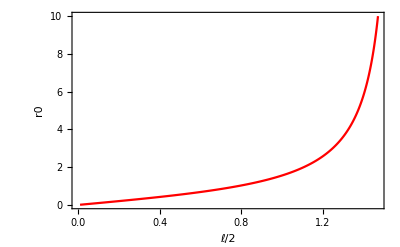

```mathematica
ListLinePlot[DisJointedTab,PlotRange->All,Frame->True,FrameLabel->{"ℓ/2","r0"},PlotStyle->{Red}](*Plot the variation of ℓ/2 with r for the disjointed solution.*)
```

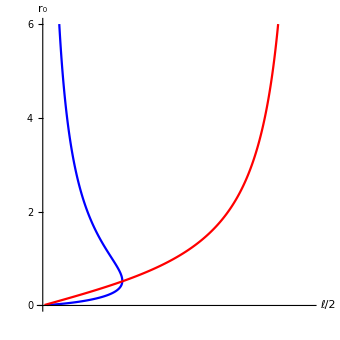

```mathematica
imager0l=ListLinePlot[{JointedTab,DisJointedTab},PlotRange->{{0,1.6},{0,6}},PlotStyle->{Blue,Red},AxesLabel->{ℓ/2,Subscript[r, 0]},AspectRatio->1,BaseStyle->texStyle,AxesLabel->MaTeX/@{"\\ell/2","r_0"},AxesOrigin->{0,0},ImageSize->12cm,AspectRatio->1,Ticks->{{{0,MaTeX[0,"DisplayStyle"->False]},{Pi/8,MaTeX[Pi/8,"DisplayStyle"->False]},{Pi/4,MaTeX[1Pi/4,"DisplayStyle"->False]},{(3Pi)/8,MaTeX[3Pi/8,"DisplayStyle"->False]},{Pi/2,MaTeX[Pi/2,"DisplayStyle"->False]}},{{0,0},{2,2},{4,4},{6,6},{8,8}}}]
```

```mathematica
tabℓactjointed=Partition[Flatten[Table[{(Pi/2-θ[100])/.NDSolve[{RHSr==LHSr,θ[r0]==Pi/2-0.0001,θ'[r0]==-80},θ,{r,r0,100}],NIntegrate[Action/.NDSolve[{RHSr==LHSr,θ[r0]==Pi/2-0.0001,θ'[r0]==-80},θ,{r,r0,100}],{r,r0,100}]},{r0,beg,end,step}],2],2];
```

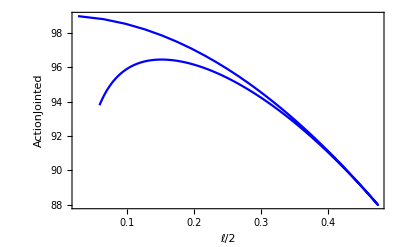

```mathematica
ListLinePlot[tabℓactjointed,PlotRange->All,Frame->True,FrameLabel->{"ℓ/2","ActionJointed"},PlotStyle->{Blue}]
```

```mathematica
(*We get two values for the action for the jointed case. corresponding to 2 possible values for r0 for each ℓ/2 value, The action for small r0 ie the surface which extends very close to the centre is never prefered as it comes with higher energy cost*)
```

```mathematica
tabℓactdisjointed=Partition[Flatten[Table[{(Pi/2-θ[100])/.NDSolve[{RHSr==LHSr,θ[r0]==0.001,θ'[r0]==80},θ,{r,r0,100}],(NIntegrate[Action/.NDSolve[{RHSr==LHSr,θ[r0]==0.001,θ'[r0]==80},θ,{r,r0,100}],{r,r0,100}])},{r0,beg,end,step}],2],2];
```

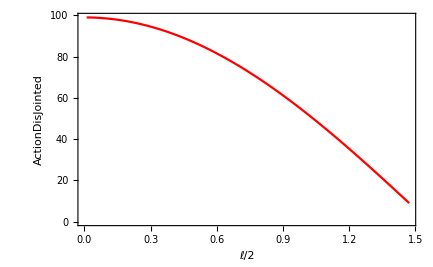

```mathematica
ListLinePlot[tabℓactdisjointed,PlotRange->All,Frame->True,FrameLabel->{"ℓ/2","ActionDisJointed"},PlotStyle->{Red}]
```

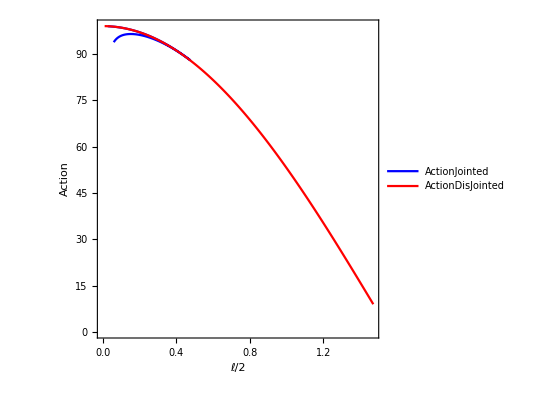

```mathematica
ListLinePlot[{tabℓactjointed,tabℓactdisjointed},PlotLegends->{"ActionJointed","ActionDisJointed"},Frame->True,FrameLabel->{"ℓ/2","Action"},PlotRange->All,PlotStyle->{Blue,Red},AspectRatio->1](**)
```

```mathematica
tabℓactjointed[[All,All]]*=2;
tabℓactdisjointed[[All,All]]*=2;
```

```mathematica
(*Estimate the Subscript[ℓ, crit]*)
curvejoin=Interpolation[tabℓactjointed];
curvedisjoin=Interpolation[tabℓactdisjointed];
FindRoot[curvejoin[x]-curvedisjoin[x],{x,0.85}]
curvedisjoin[0.8489225138536594]
```

{x→0.848923}

```mathematica
MaTeX["1.07/4"]
```

-Graphics-

FrameTicks→{{{179.5,180,180.5,181},None},{{{π/4,-Graphics-}},None}}

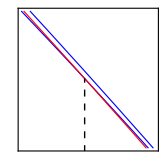

```mathematica
p1=ListLinePlot[{tabℓactjointed,tabℓactdisjointed},Frame->True,ImageSize->165,PlotRange->{{0.83,0.87},{179.5,181}},PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]}},AspectRatio->1,BaseStyle->texStyle,FrameTicks->{{{{179.5,MaTeX[179.5]},{180,MaTeX[180]},{180.5,MaTeX[180.5]},{181,MaTeX[181]}},None},{{{1.06Pi/4,MaTeX[1.06pi/4,"DisplayStyle"->False]},{1.08Pi/4,MaTeX[1.08pi/4,"DisplayStyle"->False]},{1.1Pi/4,MaTeX[1.1pi/4,"DisplayStyle"->False]}},None}},Epilog->{LineColor->Green,Dashed,Line[{{0.848922,0},{0.8489225138536594,180.26312040311205}}]}](*Demonstrates that there exists a phase transition as the action crosses between the two cases.*)
```

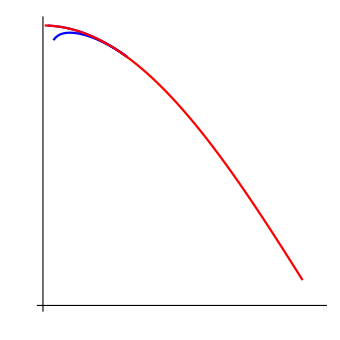

```mathematica
imagelarea=ListLinePlot[{tabℓactjointed,tabℓactdisjointed},PlotRange->{{0,3.15},{0,200}},PlotStyle->{Blue,Red},AspectRatio->1,Epilog->Inset[p1,{1,60}],BaseStyle->texStyle,AxesLabel->MaTeX/@{"\\ell","Area(\\gamma_A)"},AxesOrigin->{0,0},ImageSize->12cm,AspectRatio->1,Ticks->{{{0,MaTeX[0,"DisplayStyle"->False]},{Pi/4,MaTeX[Pi/4,"DisplayStyle"->False]},{Pi/2,MaTeX[Pi/2,"DisplayStyle"->False]},{(3Pi)/4,MaTeX[3Pi/4,"DisplayStyle"->False]},{Pi,MaTeX[Pi,"DisplayStyle"->False]}},{{0,MaTeX[0,"DisplayStyle"->False]},{50,MaTeX[50,"DisplayStyle"->False]},{100,MaTeX[100,"DisplayStyle"->False]},{150,MaTeX[150,"DisplayStyle"->False]},{200,MaTeX[200,"DisplayStyle"->False]}}}]
```

```mathematica
Export["spstripr0l.png", imager0l]
Export["spstriplarea.png", imagelarea]
```

spstripr0l.png

spstriplarea.png